## Initialization

```mathematica
Unprotect["Global`*"];
Clear["Global`*"];
ClearAll["Global`*"] ;
Remove["Global`*"] ;
Unprotect[Out];
$HistoryLength=0;
(*AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
*)
(*Print[Style["Variable Cleared",Bold,Orange]];*)
<<Notation`;
<<HaneeshPackages`;
<<NDSolve`FEM`;
(*AutoCollapse[]*)
SetDirectory[NotebookDirectory[]];
```

```mathematica
Off[Symbolize::bsymbexs];
Off[Remove::rmnsm];
λ::usage="Lame constant (double)";
μ::usage="Lame constant (double)";
t::usage="time variable";
a::usage="acceleration";
Map[Symbolize,{Subscript[u, x],Subscript[u, y],Subscript[u, z],u^x,u^y,u^z,Subscript[u, x]^h,Subscript[u, y]^h,Subscript[u, z]^h,w^x,w^y,w^z,Subscript[w, x],Subscript[w, y],Subscript[w, z],Subscript[u, x]^h,Subscript[u, y]^h,Subscript[u, z]^h}];
Map[Notation,
{u^(i_·)   ⟺  ContraVarDispU[[i_]],
u_(i_·)   ⟺  CoVarDispU[[i_]],
w^(i_·)   ⟺  ContraVarDispW[[i_]],
w_(j_·)   ⟺  CoVarDispW[[j_]],
b^(i_·)   ⟺  ContraVarb[[i_]],
b_(i_·)   ⟺  CoVarb[[i_]],
a^(i_·)   ⟺  ContraVarAccelaration[[i_]],
a_(i_·)   ⟺  CoVarAcceleration[[i_]],
x^(i_·)   ⟺  Coords[[i_]]}];
Map[ Symbolize,{N^𝔄,N^𝔅,N^ℭ,N^𝔇,N^𝔈,N^𝔉,Subscript[a, x,𝔄],Subscript[a, y,𝔅],Subscript[a, z,ℭ],Subscript[b, x,𝔇],Subscript[b, y,𝔈],Subscript[b, z,𝔉]}];
Symbolize[OverHat[x_]];
Symbolize[x̲];
Symbolize[L̄];
 Notation[g_(i_·j_·)   ⟺  CoVarMetricCoeffs[[i_,j_]]];
Notation[g^(i_·j_·)   ⟺  ContraVarMetricCoeffs[[i_,j_]]];
Notation[Γ_(i_·j_·)^(k_·)   ⟺  Γ[[i_,j_,k_]]];
Notation[u^(i_·)|_(j_·)  ⟺  CovariantDU1[i_,j_]];
Notation[u_(i_·)|_(j_·)  ⟺  CovariantDU2[i_,j_]];
Notation[w^(i_·)|_(j_·)  ⟺  CovariantDW1[i_,j_]];
Notation[w_(i_·)|_(j_·)  ⟺  CovariantDW2[i_,j_]];
Notation[γ_(i_·j_·)   ⟺  StrainCovariantU[[i_,j_]]];
Notation[ϵ_(i_·j_·)   ⟺  StrainCovariantW[[i_,j_]]];
Notation[𝔼^(i_·j_·k_·l_·)   ⟺  StiffnessContra[[i_,j_,k_,l_]]];
Notation[(∂u_)/(∂x_)   ⟺  D[u_,x_]];
Notation[τ^(i_·j_·)   ⟺  StressContra[[i_,j_]]];
Map[Symbolize,{x_^h,x_^e,Subscript[x_, i_],(x⃗)^h}];
Symbolize[Subscript[η, g]];
Symbolize[Subscript[n, x_]];
Subscript[n, el]::usage="\tNumber of Finite Elements";
Subscript[n, np]::usage="Number of Finite Element Nodes";
Subscript[n, dof]::usage="Number of degrees of freedom per node";
Subscript[n, en]::usage="Number of nodes per finite element";
Subscript[n, eq]::usage="Total Number of Equations";
Subscript[n, guass]:: usage="Number of integration points";
Symbolize[N^(i_)];Symbolize[N_(,x_)^(i_)];
Symbolize[(f⃗)_(e,a)];
(*Map[Symbolize,{Subscript[u, n+1],Subscript[u̇, n+1],Subscript[u^(..), n+1],Subscript[u, β],Subscript[u̇, β],Subscript[u^(..), β],Subscript[u, n],Subscript[u̇, n],Subscript[u^(..), n]}]*)
Map[Symbolize,{Subscript[d, n+1],Subscript[v, n+1],Subscript[a, n+1],Subscript[d̃, n+1],Subscript[ṽ, n+1],Subscript[d, n],Subscript[v, n],Subscript[a, n]}];

Subscript[d, n+1]::usage="displacement matrix at time (n+1)Δt \n \t
				 Dimensions[d_(n + 1)]= {n_eq ,1 }  ";
Subscript[v, n+1]::usage="velocity matrix at time (n+1)Δt ";
Subscript[a, n+1]::usage="acceleration matrix at time (n+1)Δt ";
Subscript[d, n]::usage="displacement matrix at time nΔt ";
Subscript[v, n]::usage="velocity matrix at time nΔt ";
Subscript[a, n]::usage="acceleration matrix at time nΔt ";
Subscript[d̃, n+1]::usage="predictor displacement matrix. \t Displacement somewhere between nΔt and (n+1)Δt  ";
Subscript[ṽ, n+1]::usage="predictor velocity matrix. \t Velocity somewhere between nΔt and (n+1)Δt  ";
(*Print[Style["New Symbols Defined",Bold,Orange]];*)
(*AutoCollapse[];*)
```

```mathematica
PrntRls={Subscript[u, 1]-> Subscript[u,1],Subscript[u, 2]-> Subscript[u,2],Subscript[u, 3]-> Subscript[u,3],
Subscript[x, 1]-> Subscript[x,1],Subscript[x, 2]-> Subscript[x,2],Subscript[x, 3]-> Subscript[x,3],
Subscript[ξ, 1]-> Subscript[ξ,1],Subscript[ξ, 2]-> Subscript[ξ,2],Subscript[ξ, 3]-> Subscript[ξ,3],
u^x-> Superscript[u,x],u^y-> Superscript[u,y],u^z-> Superscript[u,z],
Subscript[u, x]-> Subscript[u,x],Subscript[u, y]-> Subscript[u,y],Subscript[u, z]-> Subscript[u,z],
N^𝔄-> Superscript[N,𝔄],N^𝔅-> Superscript[N,𝔅],N^ℭ-> Superscript[N,ℭ],
N^𝔇-> Superscript[N,𝔇],N^𝔈-> Superscript[N,𝔈],N^𝔉-> Superscript[N,𝔉],N^(a)-> Superscript[N,"(a)"],N^(b)-> Superscript[N,"(b)"],
Subscript[a, x, 𝔄]-> Subscript[a,x,𝔄],Subscript[a, y, 𝔅]-> Subscript[a,y,𝔅],Subscript[a, z, ℭ]-> Subscript[a,z,ℭ],
Subscript[b, x, 𝔇]-> Subscript[b,x,𝔇],Subscript[b, y, 𝔈]-> Subscript[b,y,𝔈],Subscript[b, z, 𝔉]-> Subscript[b,z,𝔉],
N_(,x)^(a)->Subsuperscript[N,",x","(a)"],
N_(,y)^(a)->Subsuperscript[N,",y","(a)"],
N_(,z)^(a)->Subsuperscript[N,",z","(a)"],
N_(,x)^(b)->Subsuperscript[N,",x","(b)"],
N_(,y)^(b)->Subsuperscript[N,",y","(b)"],
N_(,z)^(b)->Subsuperscript[N,",z","(b)"],
Subscript[w, x]-> Subscript[w,x],Subscript[w, y]-> Subscript[w,y],Subscript[w, z]-> Subscript[w,z],
L̄->Overscript[L,_],Subscript[ΔT, 0]-> Subscript[ΔT,0]
};
Pprint[expri_]:=Module[{expr=expri},
expr/.PrntRls//MatrixForm//pdConv
];
Pprint[expri_,title_]:=Module[{expr=expri},
(title=expr)/.PrntRls//MatrixForm//pdConv
];

(*Print["Print Subroutines Defined"]*)
(*AutoCollapse[]*)
```

```mathematica
Guass=N@{{1/6,{1/6,1/6}},
{1/6,{2/3,1/6}},{1/6,{1/6,2/3}}};


(N^(1))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[1]];
(N^(2))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[2]];
(N^(3))[r_,s_]=ElementShapeFunction[TriangleElement,1][r,s][[3]];


(N_(,ξ)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],ξ];
(N_(,η)^(1))[ξ_,η_]=D[(N^(1))[ξ,η],η];


(N_(,ξ)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],ξ];
(N_(,η)^(2))[ξ_,η_]=D[(N^(2))[ξ,η],η];


(N_(,ξ)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],ξ];
(N_(,η)^(3))[ξ_,η_]=D[(N^(3))[ξ,η],η];
```

## Problem Formulation Theory

```mathematica
Γ=Table[0,{i,1,3},{j,1,3},{k,1,3}];
Print["Christoffel Symbols Defined"]
```

Christoffel Symbols Defined

```mathematica
CoVarMetricCoeffs={{1,0,0},{0,1,0},{0,0,1}};
ContraVarMetricCoeffs={{1,0,0},{0,1,0},{0,0,1}};

Print[Style["Covariant Metric Tensor: ",Orange]]
  Table[g_(i·j·),{i,1,3},{j,1,3}]//Pprint
Print[Style["Contravariant Metric Tensor: ",Orange]]
Table[g^(i·j·),{i,1,3},{j,1,3}]//Pprint
```

Covariant Metric Tensor:

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Contravariant Metric Tensor:

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Coords={x,y,z};
ContraVarDispU={Subscript[a, x,𝔄][t](N^𝔄)[x,y],Subscript[a, y,𝔅][t](N^𝔅)[x,y],0}; 
ContraVarAccelaration=D[ContraVarDispU,{t,2}];
ContraVarb={0,ρ g,0}; 
(*ContraVarDispU={Subscript[u, 1][x,y,z],Subscript[u, 2][x,y,z],Subscript[u, 3][x,y,z]}; *)

ContraVarDispW={Subscript[b, x,𝔇][t](N^𝔇)[x,y],Subscript[b, y,𝔈][t] (N^𝔈)[x,y],0}; 

CoVarDispU=Table[∑_(j=1)^3 (g_(i·j·)u^(j·)),{i,1,3}];
CoVarAcceleration=Table[∑_(j=1)^3 (g_(i·j·)a^(j·)),{i,1,3}];
CoVarb=Table[∑_(j=1)^3 (g_(i·j·)b^(j·)),{i,1,3}];
CoVarDispW=Table[∑_(j=1)^3 (g_(i·j·)w^(j·)),{i,1,3}];

Table[x^(i·),{i,1,3}]//Pprint
Table[u_(i·),{i,1,3}]//Pprint
Table[u^(i·),{i,1,3}]//Pprint
Table[w_(i·),{i,1,3}]//Pprint
Table[w^(i·),{i,1,3}]//Pprint
Table[b_(i·),{i,1,3}]//Pprint
Table[b^(i·),{i,1,3}]//Pprint
Table[a_(i·),{i,1,3}]//Pprint
Table[a^(i·),{i,1,3}]//Pprint
```

(x
y
z)

(a_(x,𝔄)(t) N^𝔄(x,y)
a_(y,𝔅)(t) N^𝔅(x,y)
0)

(a_(x,𝔄)(t) N^𝔄(x,y)
a_(y,𝔅)(t) N^𝔅(x,y)
0)

(b_(x,𝔇)(t) N^𝔇(x,y)
b_(y,𝔈)(t) N^𝔈(x,y)
0)

(b_(x,𝔇)(t) N^𝔇(x,y)
b_(y,𝔈)(t) N^𝔈(x,y)
0)

(0
g ρ
0)

(0
g ρ
0)

((∂^2 a_(x,𝔄)(t))/(∂t^2) N^𝔄(x,y)
(∂^2 a_(y,𝔅)(t))/(∂t^2) N^𝔅(x,y)
0)

((∂^2 a_(x,𝔄)(t))/(∂t^2) N^𝔄(x,y)
(∂^2 a_(y,𝔅)(t))/(∂t^2) N^𝔅(x,y)
0)

```mathematica
CovariantDU2[i_,j_]:=((∂u_(i·))/(∂x^(j·))-∑_(k=1)^3 (u_(k·)Γ_(i·j·)^(k·)));
StrainCovariantU=Table[1/2((u_(i·)|_(j·))+(u_(j·)|_(i·))),{i,1,3},{j,1,3}];

CovariantDW2[i_,j_]:=((∂w_(i·))/(∂x^(j·))-∑_(k=1)^3 (w_(k·)Γ_(i·j·)^(k·)));
StrainCovariantW=Table[1/2((w_(i·)|_(j·))+(w_(j·)|_(i·))),{i,1,3},{j,1,3}];

Print["Strain Tensors"]
{Flatten@FullSimplify@Table[γ_(i·j·),{i,1,3},{j,1,3}]//Pprint,Flatten@FullSimplify@Table[ϵ_(i·j·),{i,1,3},{j,1,3}]//Pprint}
```

Strain Tensors

{(a_(x,𝔄)(t) (∂N^𝔄(x,y))/(∂x)
1/2 (a_(x,𝔄)(t) (∂N^𝔄(x,y))/(∂y)+a_(y,𝔅)(t) (∂N^𝔅(x,y))/(∂x))
0
1/2 (a_(x,𝔄)(t) (∂N^𝔄(x,y))/(∂y)+a_(y,𝔅)(t) (∂N^𝔅(x,y))/(∂x))
a_(y,𝔅)(t) (∂N^𝔅(x,y))/(∂y)
0
0
0
0),(b_(x,𝔇)(t) (∂N^𝔇(x,y))/(∂x)
1/2 (b_(x,𝔇)(t) (∂N^𝔇(x,y))/(∂y)+b_(y,𝔈)(t) (∂N^𝔈(x,y))/(∂x))
0
1/2 (b_(x,𝔇)(t) (∂N^𝔇(x,y))/(∂y)+b_(y,𝔈)(t) (∂N^𝔈(x,y))/(∂x))
b_(y,𝔈)(t) (∂N^𝔈(x,y))/(∂y)
0
0
0
0)}

```mathematica
Clear[StiffnessContra];
StiffnessContra=μ Table[g^(i·r·) g^(j·s·)+g^(i·s·) g^(j·r·)+λ/μ g^(i·j·)g^(r·s·),{i,1,3},{j,1,3},{r,1,3},{s,1,3}];
Print["Stiffness Defined"]
```

Stiffness Defined

```mathematica
(*αΔT[x,z]=0;*)
StressContra=Table[∑_(r=1)^3 ∑_(s=1)^3 𝔼^(i·j·r·s·)(γ_(r·s·)-αΔT[x,y] g_(r·s·)),{i,1,3},{j,1,3}];
Print["Stress Defined"]
```

Stress Defined

```mathematica
W=Sum[τ^(i·j·)ϵ_(i·j·) ,{i,1,3},{j,1,3}]+Sum[b_(i·)w^(i·),{i,1,3}]+Sum[ρ a_(i·)w^(i·),{i,1,3}];
W=FullSimplify@W;
Print["Strain Energy Density"]
```

Strain Energy Density

```mathematica
Patt={
 x_[x,y,z] Derivative[0,1][(y_)][x,z],
x_[x,y,z] Derivative[1,0][(y_)][x,z],Derivative[1,0][(x_)][x,z]Derivative[1,0][(y_)][x,z],
Derivative[0,1][(x_)][x,y,z]Derivative[0,1][(y_)][x,z],
Derivative[0,1][(x_)][x,z]Derivative[1,0][(y_)][x,z]
x_[x,z] y_[x,z]};

Print[Style["Global Stiffness Matrix",Orange]]
K=Simplify@Outer[D[W ,#1,#2]&,{Subscript[a, x,𝔄][t],Subscript[a, y,𝔅][t],Subscript[a, z,ℭ][t]},{Subscript[b, x,𝔇][t],Subscript[b, y,𝔈][t],Subscript[b, z,𝔉][t]}];
Flatten@Table[Collect[Expand@K[[i,j]],Patt,Simplify],{i,1,3},{j,1,3}]//Pprint
```

Global Stiffness Matrix

((λ+2 μ) (∂N^𝔄(x,y))/(∂x) (∂N^𝔇(x,y))/(∂x)+μ (∂N^𝔄(x,y))/(∂y) (∂N^𝔇(x,y))/(∂y)
λ (∂N^𝔄(x,y))/(∂x) (∂N^𝔈(x,y))/(∂y)+μ (∂N^𝔄(x,y))/(∂y) (∂N^𝔈(x,y))/(∂x)
0
λ (∂N^𝔅(x,y))/(∂y) (∂N^𝔇(x,y))/(∂x)+μ (∂N^𝔅(x,y))/(∂x) (∂N^𝔇(x,y))/(∂y)
(λ+2 μ) (∂N^𝔅(x,y))/(∂y) (∂N^𝔈(x,y))/(∂y)+μ (∂N^𝔅(x,y))/(∂x) (∂N^𝔈(x,y))/(∂x)
0
0
0
0)

```mathematica
M=Simplify@Outer[D[W ,#1,#2]&,{Subscript[a, x,𝔄]''[t],Subscript[a, y,𝔅]''[t],Subscript[a, z,ℭ]''[t]},{Subscript[b, x,𝔇][t],Subscript[b, y,𝔈][t],Subscript[b, z,𝔉][t]}];
Table[Collect[Expand@M[[i,j]],Patt,Simplify],{i,1,3},{j,1,3}]//Pprint
```

(ρ N^𝔄(x,y) N^𝔇(x,y) | 0 | 0
0 | ρ N^𝔅(x,y) N^𝔈(x,y) | 0
0 | 0 | 0)

```mathematica
F=Simplify@Map[D[(W /.{Subscript[a, x,𝔄][t]->0,Subscript[a, y,𝔅][t]->0,Subscript[a, z,ℭ][t]->0,Subscript[a, x,𝔄]''[t]->0,Subscript[a, y,𝔅]''[t]->0,Subscript[a, z,ℭ]''[t]->0}),#]&,{Subscript[b, x,𝔇][t],Subscript[b, y,𝔈][t],Subscript[b, z,𝔉][t]}];
Print[Style["Global Force Matrix",Orange]]
Flatten@Table[Collect[Expand@F[[i]],Patt,Simplify],{i,1,3}]//Pprint
```

Global Force Matrix

(-(3 λ+2 μ) αΔT(x,y) (∂N^𝔇(x,y))/(∂x)
g ρ N^𝔈(x,y)-(3 λ+2 μ) αΔT(x,y) (∂N^𝔈(x,y))/(∂y)
0)

```mathematica
k^e=K/.((Derivative[0,0,1][(N^𝔄)])[x,y] | (Derivative[0,0,1][(N^𝔅)])[x,y] | (Derivative[0,0,1][(N^ℭ)])[x,y])-> (N_(,z)^(a))[ξ,η]/.
((Derivative[0,1][(N^𝔄)])[x,y] | (Derivative[0,1][(N^𝔅)])[x,y] | (Derivative[0,1][(N^ℭ)])[x,y])-> (N_(,y)^(a))[ξ,η]/.
((Derivative[1,0][(N^𝔄)])[x,y] | (Derivative[1,0][(N^𝔅)])[x,y] | (Derivative[1,0][(N^ℭ)])[x,y])-> (N_(,x)^(a))[ξ,η]/.
((N^𝔄)[x,y]| (N^𝔅)[x,y] | (N^ℭ)[x,y])->(N^(a))[ξ,η]/.
((Derivative[0,0,1][(N^𝔇)])[x,y]| (Derivative[0,0,1][(N^𝔈)])[x,y] | (Derivative[0,0,1][(N^𝔉)])[x,y])-> (N_(,z)^(b))[ξ,η]/.
((Derivative[0,1][(N^𝔇)])[x,y]| (Derivative[0,1][(N^𝔈)])[x,y] | (Derivative[0,1][(N^𝔉)])[x,y])-> (N_(,y)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[x,y]| (Derivative[1,0][(N^𝔈)])[x,y] | (Derivative[1,0][(N^𝔉)])[x,y])-> (N_(,x)^(b))[ξ,η]/.
((N^𝔇)[x,y]| (N^𝔈)[x,y] | (N^𝔉)[x,y])->(N^(b))[ξ,η];
k^e//Pprint
```

((λ+2 μ) N_(,x)^(a)(ξ,η) N_(,x)^(b)(ξ,η)+μ N_(,y)^(a)(ξ,η) N_(,y)^(b)(ξ,η) | λ N_(,x)^(a)(ξ,η) N_(,y)^(b)(ξ,η)+μ N_(,y)^(a)(ξ,η) N_(,x)^(b)(ξ,η) | 0
λ N_(,y)^(a)(ξ,η) N_(,x)^(b)(ξ,η)+μ N_(,x)^(a)(ξ,η) N_(,y)^(b)(ξ,η) | μ N_(,x)^(a)(ξ,η) N_(,x)^(b)(ξ,η)+(λ+2 μ) N_(,y)^(a)(ξ,η) N_(,y)^(b)(ξ,η) | 0
0 | 0 | 0)

```mathematica
m^e=M/.((Derivative[0,0,1][(N^𝔄)])[x,y] | (Derivative[0,0,1][(N^𝔅)])[x,y] | (Derivative[0,0,1][(N^ℭ)])[x,y])-> (N_(,z)^(a))[ξ,η]/.
((Derivative[0,1][(N^𝔄)])[x,y] | (Derivative[0,1][(N^𝔅)])[x,y] | (Derivative[0,1][(N^ℭ)])[x,y])-> (N_(,y)^(a))[ξ,η]/.
((Derivative[1,0][(N^𝔄)])[x,y] | (Derivative[1,0][(N^𝔅)])[x,y] | (Derivative[1,0][(N^ℭ)])[x,y])-> (N_(,x)^(a))[ξ,η]/.
((N^𝔄)[x,y]| (N^𝔅)[x,y] | (N^ℭ)[x,y])->(N^(a))[ξ,η]/.
((Derivative[0,0,1][(N^𝔇)])[x,y]| (Derivative[0,0,1][(N^𝔈)])[x,y] | (Derivative[0,0,1][(N^𝔉)])[x,y])-> (N_(,z)^(b))[ξ,η]/.
((Derivative[0,1][(N^𝔇)])[x,y]| (Derivative[0,1][(N^𝔈)])[x,y] | (Derivative[0,1][(N^𝔉)])[x,y])-> (N_(,y)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[x,y]| (Derivative[1,0][(N^𝔈)])[x,y] | (Derivative[1,0][(N^𝔉)])[x,y])-> (N_(,x)^(b))[ξ,η]/.
((N^𝔇)[x,y]| (N^𝔈)[x,y] | (N^𝔉)[x,y])->(N^(b))[ξ,η];
m^e//Pprint
```

(ρ N^(a)(ξ,η) N^(b)(ξ,η) | 0 | 0
0 | ρ N^(a)(ξ,η) N^(b)(ξ,η) | 0
0 | 0 | 0)

```mathematica
f^e=F/.((Derivative[0,0,1][(N^𝔄)])[x,y] | (Derivative[0,0,1][(N^𝔅)])[x,y] | (Derivative[0,0,1][(N^ℭ)])[x,y])-> (N_(,z)^(a))[ξ,η]/.
((Derivative[0,1][(N^𝔄)])[x,y] | (Derivative[0,1][(N^𝔅)])[x,y] | (Derivative[0,1][(N^ℭ)])[x,y])-> (N_(,y)^(a))[ξ,η]/.
((Derivative[1,0][(N^𝔄)])[x,y] | (Derivative[1,0][(N^𝔅)])[x,y] | (Derivative[1,0][(N^ℭ)])[x,y])-> (N_(,x)^(a))[ξ,η]/.
((N^𝔄)[x,y]| (N^𝔅)[x,y] | (N^ℭ)[x,y])->(N^(a))[ξ,η]/.
((Derivative[0,0,1][(N^𝔇)])[x,y]| (Derivative[0,0,1][(N^𝔈)])[x,y] | (Derivative[0,0,1][(N^𝔉)])[x,y])-> (N_(,z)^(b))[ξ,η]/.
((Derivative[0,1][(N^𝔇)])[x,y]| (Derivative[0,1][(N^𝔈)])[x,y] | (Derivative[0,1][(N^𝔉)])[x,y])-> (N_(,y)^(b))[ξ,η]/.((Derivative[1,0][(N^𝔇)])[x,y]| (Derivative[1,0][(N^𝔈)])[x,y] | (Derivative[1,0][(N^𝔉)])[x,y])-> (N_(,x)^(b))[ξ,η]/.
((N^𝔇)[x,y]| (N^𝔈)[x,y] | (N^𝔉)[x,y])->(N^(b))[ξ,η];
f^e//Pprint
```

(-(3 λ+2 μ) αΔT(x,y) N_(,x)^(b)(ξ,η)
g ρ N^(b)(ξ,η)-(3 λ+2 μ) αΔT(x,y) N_(,y)^(b)(ξ,η)
0)

## Problem Solution: Numerics

## Numerics subroutine:

```mathematica
ClearAll[Subscript[SetUpη, g]];
Subscript[SetUpη, g][Coordinates0_,tol_:0.0001]:=Module[{Coordinates=Coordinates0,Subscript[n, np], Subscript[x, i],Subscript[y, i],Subscript[η, g],Subscript[y, 0],Subscript[x, 0],Subscript[x, 1]},
Subscript[n, np]=Length@Coordinates;
Subscript[x, 0]=0.0;
Subscript[y, 0]=0.0;
Subscript[y, 1]=1.81; (*need to take care of this when changing the sample size*)
Subscript[η, g]={{},{}};
For[i=1,i<Subscript[n, np],i++,
{Subscript[x, i],Subscript[y, i]}=Coordinates[[i]];

If[(Abs[Subscript[x, i]-Subscript[x, 0]]≤tol)∨(Abs[Subscript[y, i]-Subscript[y, 1]]≤tol), AppendTo[Subscript[η, g][[1]],i]];
If[Abs[Subscript[y, i]-Subscript[y, 1]]≤tol, AppendTo[Subscript[η, g][[2]],i]];

];
Subscript[η, g] 
]
```

```mathematica
ClearAll[SetUpηVals];
SetUpηVals[Subscript[η, g]:_ , û:_, v̂:_]:=Module[{𝒾,ηVals,NumberOfηNodes,ηFuncs={û,v̂},A,𝓅,Subscript[x, 1],Subscript[x, 2]},
ηVals={{},{}};
NumberOfηNodes=Map[Length,Subscript[η, g][[;;]]];
For[𝒾=1,𝒾≤ Subscript[n, dof],𝒾++,
For[𝓅=1,𝓅≤NumberOfηNodes[[𝒾]],𝓅++,
A=Subscript[η, g][[𝒾,𝓅]];
{Subscript[x, 1],Subscript[x, 2]}=((x⃗)^h)[[A]];
AppendTo[ηVals[[𝒾]],A->ηFuncs[[𝒾]][{Subscript[x, 1],Subscript[x, 2]}]];
];
];
ηVals
]
```

```mathematica
ClearAll[SetUpIDArray];
SetUpIDArray[]:=Module[{P,A,i,j,ID},
ID=Table[0,{i,1,Subscript[n, dof]},{j,1,Subscript[n, np]}];
P=1;
For[A=1,A≤ Subscript[n, np],A++,
For[i=1,i≤ Subscript[n, dof],i++,
If[!MemberQ[Subscript[η, g][[i]],A],ID[[i,A]]=P;P=P+1,ID[[i,A]]=0];
];
];
ID
]
```

```mathematica
GetElement[e_]:=Module[{𝒜, ℬ, 𝒞,p1,p2,p3},
𝒜=IEN[[1,e]];
ℬ=IEN[[2,e]];
𝒞=IEN[[3,e]];
p1=((x⃗)^h)[[𝒜]];
p2=((x⃗)^h)[[ℬ]];
p3=((x⃗)^h)[[𝒞]];
ToElementMesh["Coordinates"->{p1,p2,p3},"MeshElements"-> 
{TriangleElement[{{1,2,3}}]}]
]
```

```mathematica
SplitSolution[sol0_]:=Module[{sol=sol0,e,a,i,A,P,UMat},
UMat=SparseArray[{},{Subscript[n, np],Subscript[n, dof]},0.0];
For[e=1,e ≤ Subscript[n, el],e++, 
For[a=1,a≤ Subscript[n, en],a++,
For[i=1,i≤ Subscript[n, dof],i++,
A=IEN[[a,e]];
P=ID[[i,A]];
If[P≠ 0,UMat[[A,i]]=sol[[P]]];
If[P== 0,UMat[[A,i]]=A/.ηVals[[i]]]
]
]
];
UMat
]
```

```mathematica
Clear[k^e, G^e, f^e];
(k^e)[{ξ:_,η:_},{x_,y_},{N_(,x)^(a):_,N_(,y)^(a):_},{N_(,x)^(b):_,N_(,y)^(b):_},{N^(a):_},{N^(b):_}]:={{(λ+2 μ) ((N_(,x)^(a))[ξ,η] (N_(,x)^(b))[ξ,η]+1/x^2(N^(a))[ξ,η](N^(b))[ξ,η])+μ (N_(,y)^(a))[ξ,η] (N_(,y)^(b))[ξ,η]+λ/x((N^(a))[ξ,η](N_(,x)^(b))[ξ,η]+(N_(,x)^(a))[ξ,η](N^(b))[ξ,η]),μ (N_(,x)^(b))[ξ,η] (N_(,y)^(a))[ξ,η]+λ (N_(,x)^(a))[ξ,η] (N_(,y)^(b))[ξ,η]+λ/x(N^(a))[ξ,η](N_(,y)^(b))[ξ,η]},{λ (N_(,x)^(b))[ξ,η] (N_(,y)^(a))[ξ,η]+μ (N_(,x)^(a))[ξ,η] (N_(,y)^(b))[ξ,η]+λ/x(N_(,y)^(a))[ξ,η](N^(b))[ξ,η],μ (N_(,x)^(a))[ξ,η] (N_(,x)^(b))[ξ,η]+(λ+2 μ) (N_(,y)^(a))[ξ,η] (N_(,y)^(b))[ξ,η]}};
(G^e)[{ξ:_,η:_},{x_,y_},{N^(a):_},{N^(b):_}]:={{0,0},{0, (N^(a))[ξ,η] (N^(b))[ξ,η]}};
(f^e)[{ξ_,η_},{x_,y_},{ N^(b):_}]:={0, (N^(b))[ξ,η]};
```

```mathematica
CalculateGuassPoints[e0_]:=Module[{e=e0,P,Q,R,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],GuassPointsSpatial,GuassPointsNatural,GuassWeights,i,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i]},
{P,Q,R}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}=((x⃗)^h)[[{P,Q,R}]];
GuassWeights={};
GuassPointsSpatial={};
GuassPointsNatural={};
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]}}=Guass[[i]];
{Subscript[x, i],Subscript[y, i]}={
(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[x, 3],
(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[y, 3]};
AppendTo[GuassPointsSpatial,{Subscript[x, i],Subscript[y, i]}];
AppendTo[GuassPointsNatural,{Subscript[ξ, i],Subscript[η, i]}];
AppendTo[GuassWeights,Subscript[w, i]];
];
Remove[e,P,Q,R,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],i,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i]];
{GuassWeights,GuassPointsNatural,GuassPointsSpatial}
]
```

```mathematica
ElementJacobian[e0_,j^e:_,B^e:_]:=Module[{e=e0,P,Q,R,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],J^e},
{P,Q,R}=IEN[[;;,e]];
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}=((x⃗)^h)[[{P,Q,R}]];
J^e={{-Subscript[x, 1]+Subscript[x, 2],-Subscript[y, 1]+Subscript[y, 2]},{-Subscript[x, 1]+Subscript[x, 3],-Subscript[y, 1]+Subscript[y, 3]}};
j^e=Det[J^e];
(B^e)[ξ_,η_]= Inverse[J^e].({{(N_(,ξ)^(1))[ξ,η], (N_(,ξ)^(2))[ξ,η], (N_(,ξ)^(3))[ξ,η]}, {(N_(,η)^(1))[ξ,η], (N_(,η)^(2))[ξ,η], (N_(,η)^(3))[ξ,η]}});
Remove[e,P,Q,R,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],J^e];
Return[]  
]
```

```mathematica
GuassIntegrate[e0_Integer,f0_]:=Module[{e=e0,f=f0,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i],ℐ=0,GuassPoints},
GuassPoints=CalculateGuassPoints[e];
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]},{Subscript[x, i],Subscript[y, i]}}=GuassPoints[[;;,i]];
ℐ+=(2π Subscript[x, i])*Subscript[w, i] f[{Subscript[ξ, i],Subscript[η, i]},{Subscript[x, i],Subscript[y, i]}](*An additional term (2π Subscript[x, i]) due to the axisymmeric integral*)
];
Remove[e,f,Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i],GuassPoints];
ℐ
]
```

```mathematica
ComputeElementStiffnessMatrix[e0_]:=Module[{e=e0,A,B,P,Q, 𝒾,𝒿,a,b,x,y,ξ,η,j^e,B^e,ℐ=0.0,f,N_(,x)^(a),N_(,y)^(a),N_(,x)^(b),N_(,y)^(b),N^(a),N^(b)},
ElementJacobian[e,j^e,B^e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
{(N_(,x)^(a))[ξ_,η_],(N_(,y)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
{(N_(,x)^(b))[ξ_,η_],(N_(,y)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];

For[𝒾=1,𝒾≤ Subscript[n, dof],𝒾++,
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{x_,y_}]=j^e(k^e)[{ξ,η},{x,y},{N_(,x)^(a),N_(,y)^(a)},{N_(,x)^(b),N_(,y)^(b)},{N^(a)},{N^(b)}][[𝒾,𝒿]];
(*I missed the arguments {N^(a)},{N^(b)} in the previous version so that the result was not right*)
ℐ=GuassIntegrate[e,f];

A=IEN[[a,e]];
B=IEN[[b,e]];
P=ID[[𝒾,A]];Q=ID[[𝒿,B]];
If[P≠0 && Q≠ 0,KMat[[P,Q]]+=ℐ];
If[ P≠ 0 &&  Q== 0,fMat1[[P]]+=- ℐ (B/.ηVals[[𝒿]])];
If[ P== 0 &&  Q≠  0,fMat1[[Q]]+= -ℐ (A/.ηVals[[𝒾]])]
];
];
];
];
Remove[A,B,P,Q, 𝒾,𝒿,a,b,x,y,ξ,η,j^e,B^e,ℐ,f,N_(,x)^(a),N_(,y)^(a),N_(,x)^(b),N_(,y)^(b),N^(a),N^(b)];
{e,$KernelID}
]
```

```mathematica
GetDisplacement[e_]:=Module[{p,q,r,U1,U2,U3,V1,V2,V3},
{p,q,r}=IEN[[;;,e]];
{{U1,V1},{U2,V2},{U3,V3}}=uMatNR[[{p,q,r}]];
Remove[p,q,r];
{{U1,V1},{U2,V2},{U3,V3}}
]
```

```mathematica
ComputeElementStiffnessMatrixFromBodyforce[{e0_,h_}]:=Module[{e=e0,A,B,P,Q, 𝒾,𝒿,a,b,x,y,ξ,η,j^e,B^e,Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[v, 1],Subscript[v, 2],Subscript[v, 3],ℐ=0.0,f,N^(a),N^(b),Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i],ri,LJBFD,GuassPoints},
ElementJacobian[e,j^e,B^e];
GuassPoints=CalculateGuassPoints[e];
{{Subscript[u, 1],Subscript[v, 1]},{Subscript[u, 2],Subscript[v, 2]},{Subscript[u, 3],Subscript[v, 3]}}=GetDisplacement[e];

For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];

For[𝒾=1,𝒾≤ Subscript[n, dof],𝒾++,
For[𝒿=1,𝒿≤ Subscript[n, dof],𝒿++,
f[{ξ_,η_},{x_,y_}]=j^e(G^e)[{ξ,η},{x,y},{N^(a)},{N^(b)}][[𝒾,𝒿]];
(*ℐ=GuassIntegrate[e,f];*)
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]},{Subscript[x, i],Subscript[y, i]}}=GuassPoints[[;;,i]];
{Subscript[u, i],Subscript[v, i]}={(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[u, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[u, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[u, 3], (N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[v, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[v, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[v, 3]};
ri=Subscript[y, i]+Subscript[v, i]-h;
LJBFD=Piecewise[{{0, ri≤Rc}, {(8Am)/Σ(-C12(Σ/ri)^11+C6(Σ/ri)^5), Rc<ri≤R1}, {c2+2c3(ri-R1)+3c4(ri-R1)^2, R1<ri≤R2}, {0, ri>R2}}];
ℐ+=(2π Subscript[x, i])*Subscript[w, i] f[{Subscript[ξ, i],Subscript[η, i]},{Subscript[x, i],Subscript[y, i]}]*LJBFD(*An additional term (2π Subscript[x, i]) due to the axisymmeric integral*)
];

A=IEN[[a,e]];
B=IEN[[b,e]];
P=ID[[𝒾,A]];Q=ID[[𝒿,B]];
If[P≠0 && Q≠ 0,GMat[[P,Q]]+=ℐ];
If[ P≠ 0 &&  Q== 0,fMat2[[P]]+=- ℐ (B/.ηVals[[𝒿]])];
If[ P== 0 &&  Q≠  0,fMat2[[Q]]+= -ℐ (A/.ηVals[[𝒾]])];
ℐ=0(*need to reset ℐ at this point*)
];
];
];
];
Remove[e,A,B,P,Q, 𝒾,𝒿,a,b,x,y,ξ,η,j^e,B^e,Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[v, 1],Subscript[v, 2],Subscript[v, 3],ℐ,f,N^(a),N^(b),Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i],ri,LJBFD,GuassPoints];
{e,$KernelID}
]
```

```mathematica
ComputeGlobalForceMatrixFromBodyforce[{e0_,h_}]:=Module[{e=e0,B,Q,𝒿,b,x,y,ξ,η,j^e,B^e,Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[v, 1],Subscript[v, 2],Subscript[v, 3],ℐ=0.0,f,N^(a),N^(b),Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i],ri,LJBF,GuassPoints},
ElementJacobian[e,j^e,B^e];
GuassPoints=CalculateGuassPoints[e];
{{Subscript[u, 1],Subscript[v, 1]},{Subscript[u, 2],Subscript[v, 2]},{Subscript[u, 3],Subscript[v, 3]}}=GetDisplacement[e];

For[b=1,b≤Subscript[n, en],b++,
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
For[𝒿=1,𝒿≤Subscript[n, dof],𝒿++,
f[{ξ_,η_},{x_,y_}]=j^e(f^e)[{ξ,η},{x,y},{N^(b)}][[𝒿]];
(*ℐ=GuassIntegrate[e,f];*)
For[i=1,i≤ Subscript[n, guass],i++,
{Subscript[w, i],{Subscript[ξ, i],Subscript[η, i]},{Subscript[x, i],Subscript[y, i]}}=GuassPoints[[;;,i]];
{Subscript[u, i],Subscript[v, i]}={(N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[u, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[u, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[u, 3], (N^(1))[Subscript[ξ, i],Subscript[η, i]] Subscript[v, 1]+(N^(2))[Subscript[ξ, i],Subscript[η, i]] Subscript[v, 2]+(N^(3))[Subscript[ξ, i],Subscript[η, i]] Subscript[v, 3]};
ri=Subscript[y, i]+Subscript[v, i]-h;
LJBF=Piecewise[{{Am((4C12)/5(Σ/Rc)^10-2C6(Σ/Rc)^4), ri≤Rc}, {Am((4C12)/5(Σ/ri)^10-2C6(Σ/ri)^4), Rc<ri≤R1}, {c1+c2(ri-R1)+c3(ri-R1)^2+c4(ri-R1)^3, R1<ri≤R2}, {0, ri>R2}}];
ℐ+=(2π Subscript[x, i])*Subscript[w, i] f[{Subscript[ξ, i],Subscript[η, i]},{Subscript[x, i],Subscript[y, i]}]*LJBF(*An additional term (2π Subscript[x, i]) due to the axisymmeric integral*)
];

ClearAll[f];
B=IEN[[b,e]];
Q=ID[[𝒿,B]];
If[ Q≠ 0,fMat3[[Q]]+=ℐ];
ℐ=0 (*need to reset ℐ at this point*)
];
];
Remove[e,B,Q,𝒿,b,x,y,ξ,η,j^e,B^e,Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[v, 1],Subscript[v, 2],Subscript[v, 3],ℐ,f,N^(a),N^(b),Subscript[w, i],Subscript[ξ, i],Subscript[η, i],Subscript[x, i],Subscript[y, i],ri,LJBF,GuassPoints];
{e,$KernelID}
]
```

```mathematica
ClearAll[a^e,l^e,ComputeGlobalForceMatrixForStressProjection,ComputeElementStiffnessMatrixForStressProjection];
(*I have not checked this subroutine for stress plot*)
ComputeElementStiffnessMatrixForStressProjection[e0_]:=Module[{e=e0,A,B,P,Q,a,b,ξ,η,j^e,B^e,ℐ=0.0,f,N^(a),N^(b)},
ElementJacobian[e,j^e,B^e];
For[a=1,a≤ Subscript[n, en],a++,
For[b=1,b≤ Subscript[n, en],b++,
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
f[{ξ_,η_},{x_,y_}]=(N^(a))[ξ,η](N^(b))[ξ,η];
ℐ=j^e GuassIntegrate[e,f];
A=IEN[[a,e]];
B=IEN[[b,e]];
aMat[[A,B]]+=ℐ;
];
];
Remove[e,A,B,P,Q,a,b,ξ,η,j^e,B^e,ℐ,f,N^(a),N^(b)];
{e,$KernelID}
]

ComputeGlobalForceMatrixForStressProjection[e0_]:=Module[{e=e0,A,B,a,b,ξ,η,j^e,B^e,f,N_(,x)^(a),N_(,y)^(a),N_(,x)^(b),N_(,y)^(b),N^(a),N^(b),ℐ11,ℐ12,ℐ21,ℐ22},
ElementJacobian[e,j^e,B^e];
For[a=1,a≤ Subscript[n, en],a++,
{(N_(,x)^(a))[ξ_,η_],(N_(,y)^(a))[ξ_,η_]}=(B^e)[ξ,η][[;;,a]];
(N^(a))[ξ_,η_]=NMat[ξ,η][[a]];
ℐ11=ℐ12=ℐ21=ℐ22=0;
A=IEN[[a,e]];
For[b=1,b≤ Subscript[n, en],b++,
B=IEN[[b,e]];
{(N_(,x)^(b))[ξ_,η_],(N_(,y)^(b))[ξ_,η_]}=(B^e)[ξ,η][[;;,b]];
(N^(b))[ξ_,η_]=NMat[ξ,η][[b]];
ClearAll[f];
f[{ξ_,η_},{x_,y_}]=(N^(a))[ξ,η](N_(,x)^(b))[ξ,η];
ℐ11+=j^e UMat[[B,1]]GuassIntegrate[e,f];
ℐ21+=j^e UMat[[B,2]]GuassIntegrate[e,f];
ClearAll[f];
f[{ξ_,η_},{x_,y_}]=(N^(a))[ξ,η](N_(,y)^(b))[ξ,η];
ℐ12+=j^e UMat[[B,1]]GuassIntegrate[e,f];
ℐ22+=j^e UMat[[B,2]]GuassIntegrate[e,f];
];
l11Mat[[A]]+=ℐ11;
l21Mat[[A]]+=ℐ21;
l12Mat[[A]]+=ℐ12;
l22Mat[[A]]+=ℐ22;
];
Remove[e,A,B,a,b,ξ,η,j^e,B^e,f,N_(,x)^(a),N_(,y)^(a),N_(,x)^(b),N_(,y)^(b),N^(a),N^(b)];
{e,$KernelID}
]
```

## Define Geometry Dimensions and Material Properties

```mathematica
Unprotect[λ,μ,Ω^h,α,ρ,g, αΔT,Ε,ν,Subscript[A, LJ],Σ,Am,Subscript[k, c]];
ClearAll[λ,μ,Ω^h,α,ρ,g, αΔT,Ε,ν,Subscript[A, LJ],Σ,Am,Subscript[k, c]];
<<NDSolve`FEM`
λ= 2*4.4 10^5;
μ=2*4.4 10^5;
Ε=(μ(3λ+2μ))/(λ+μ);
ν=λ/(2(λ+μ));

Subscript[A, LJ]=(3.)^2*10^-3;
Σ=3. 10^-3;
Am=Subscript[A, LJ]/(4π Σ^4);
Subscript[k, c]=0.475;
Rc=Subscript[k, c] Σ;
R1=2.Σ;
R2=3.Σ;
C6=3.;
C12=1.;
c1=Am((4C12)/5(Σ/R1)^10-2C6(Σ/R1)^4);
c2=(8Am)/Σ(-C12(Σ/R1)^11+C6(Σ/R1)^5);
c3=-(3c1-2c2 R1+2c2 R2)/(R1-R2)^2;
c4=-(2c1-c2 R1+c2 R2)/(R1-R2)^3;

ρ=0.0;
g=0.0;
αΔT[x_,y_]=0.0;
```

```mathematica
pwd=SetDirectory[NotebookDirectory[]];
(*savedir=CreateDirectory[FileNameJoin[{pwd,"C12=1.0HW"}]];
SetDirectory[savedir]*)
```

```mathematica
width = 6.;
height = 1.8;
radius = 10; 
ydatum = 0.01;
Aw=0. 10^-3;
λw=0.125;
ℛ=ImplicitRegion[(0≤x≤width/2 )&& (y≤height+ydatum) &&( y≥x^2/(2radius)+Aw(1-Cos[(2π x)/λw])+ydatum),{{x,-0.1,width/2+0.1},{y,0,height+0.1}}];
(*RegionPlot[ℛ,AspectRatio->Automatic,ImageSize->Large]*)

meshrefine=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[Aw(1-Cos[(2π x)/λw])+ydatum≤ y≤x^2/(2.4 radius)+Aw(1-Cos[(2π x)/λw])+ydatum+0.012,area>14. 10^-7,area>0.001]]];
Ω^h=ToElementMesh[ℛ,MaxCellMeasure->0.0003,"MeshElementType"->"TriangleElement","MeshOrder"->1,MeshRefinementFunction->meshrefine,AccuracyGoal->4.]
Export["meshdata.txt",NumberForm[#,ExponentFunction->(Null&)]&/@List@@(Ω^h),"String"]
```

ElementMesh[{{0.,3.},{0.01,1.81}},{TriangleElement[<39889>]}]

meshdata.txt

{{0.601327},{0.912637},{0.0775938}}

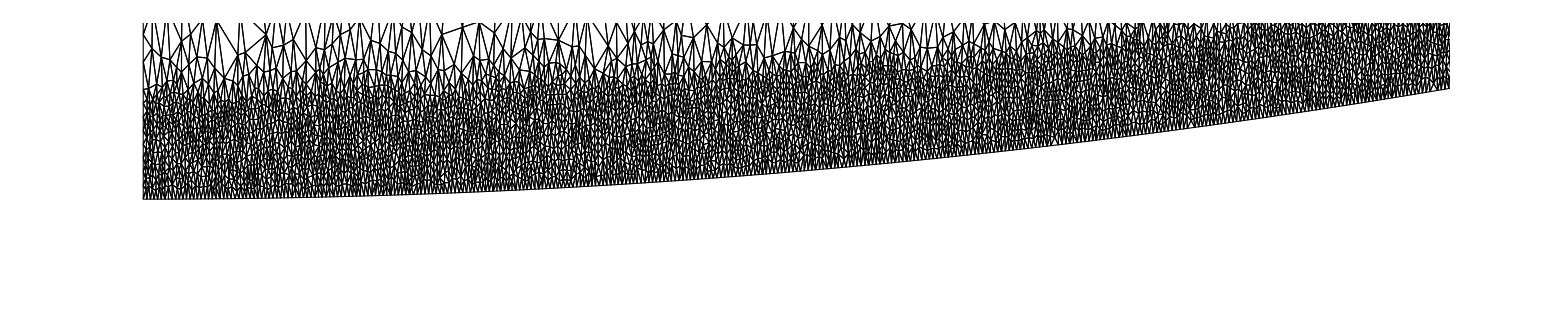

```mathematica
meshIn=#1->#2&~MapThread~{{"Coordinates","MeshElements","BoundaryElements","PointElements"},ToExpression@Import["meshdata.txt"]}//ToElementMesh@@#&;
q=meshIn["Quality"];
{Min/@q,Mean/@q,StandardDeviation/@q}
Show[meshIn["Wireframe"],PlotRange->{{0.,0.5},{0,0.03}},ImageSize->2000]
```

```mathematica
pos=Position[q,_?(#≤0.6&)];
Show[meshIn["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[GrayLevel[.9]],FaceForm[]]]],meshIn["Wireframe"[pos,"MeshElement"->"MeshElements","ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],Boxed->False,PlotRange->{{0.0,0.5},{0,0.03-ydatum}},ImageSize->800]
```

-Graphics-

## Create Mesh and Mesh Data Structures

```mathematica
Unprotect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh,NMat,Subscript[ηElements, g],ηVals];
ClearAll[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,NMat,Subscript[ηElements, g],ηVals];
(x⃗)^h=(Ω^h)["Coordinates"];
Subscript[n, np]=Length@((x⃗)^h);
IEN=Apply[List,(Ω^h)["MeshElements"],{1}][[1,1]]ᵀ ;
NMat[ξ_,η_]={(N^(1))[ξ,η],(N^(2))[ξ,η],(N^(3))[ξ,η]};
Subscript[n, en]=Dimensions[IEN][[1]];
Subscript[n, el]=Dimensions[IEN][[2]];
Subscript[n, dof]=2;
Subscript[n, guass]=3;
Subscript[η, g]=Subscript[SetUpη, g][(x⃗)^h] ;

û[{Subscript[x, 1]:_,Subscript[x, 2]:_}]=0.0;
v̂[{Subscript[x, 1]:_,Subscript[x, 2]:_}]=0.0;

ηVals=SetUpηVals[Subscript[η, g], û, v̂];
ID=SetUpIDArray[];
Subscript[n, eq]=Max[ID]
(Ω^h)["PointElements"]={PointElement[Table[{i},{i,1,Subscript[n, np]}]]};
Protect[Subscript[n, np],Subscript[n, en],Subscript[n, el],Subscript[n, dof],Subscript[n, guass],Subscript[η, g],Subscript[n, eq],IEN,ID,ElementMesh, NMat,Subscript[ηElements, g],ηVals];
```

40679

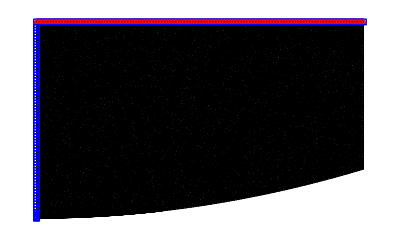

```mathematica
Show[(Ω^h)["Wireframe"["MeshElement" -> "MeshElements"]],
ListPlot[((x⃗)^h)[[Subscript[η, g][[1]]]],PlotMarkers->Style["□",Blue]],ListPlot[((x⃗)^h)[[Subscript[η, g][[2]]]],PlotMarkers->Style["△",Red]],ImageSize->Full]
```

```mathematica
Protect[λ,μ,Ω^h,α,ρ,g,αΔT,Ε,ν,Subscript[A, LJ],Σ,Subscript[A, m],Subscript[k, c]];
```

```mathematica
ParallelEvaluate[$KernelID];
nKernel=$KernelCount
DistributeDefinitions[GuassIntegrate,ElementJacobian,CalculateGuassPoints,SplitSolution,GetDisplacement,IEN,ID,λ,μ,k^e,G^e,f^e,NMat,uOld,ComputeElementStiffnessMatrix,ComputeElementStiffnessMatrixFromBodyforce,ComputeGlobalForceMatrixFromBodyforce]
```

34

{GuassIntegrate,CalculateGuassPoints,y_1,i,IEN,(x⃗)^h,n_guass,Guass,N^(1),N^(2),N^(3),ElementJacobian,N_(,ξ)^(1),N_(,ξ)^(2),N_(,ξ)^(3),N_(,η)^(1),N_(,η)^(2),N_(,η)^(3),SplitSolution,a,n_np,n_dof,n_el,n_en,ID,ηVals,GetDisplacement,q,λ,μ,k^e,G^e,f^e,NMat,ComputeElementStiffnessMatrix,ComputeElementStiffnessMatrixFromBodyforce,Rc,Am,Σ,C12,C6,R1,c2,c3,c4,R2,ComputeGlobalForceMatrixFromBodyforce,c1}

## Loading step

```mathematica
hvec={1.0,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.0,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.0,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.0,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.0,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.0,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.0,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.0,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.0,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16}*10^-3;
nStep=Length@hvec
DisplUMat=Table[0,{i,1,nStep},{j,1,Subscript[n, eq]}];
```

151

```mathematica
PrntlLoadLog[step_,iter_,nl_,dU_,dt_]:=Module[{},
loginfo=StringJoin[ToString[iter],"   Residual: ",ToString[nl,InputForm],"   Correction: ",ToString[dU,InputForm],"   time: ",ToString[dt],"\n"];
filename=FileNameJoin[{"Load.log"}];
str=OpenAppend[filename];
If[iter==0,WriteString[str,StringJoin["Step ",ToString[step]," ",DateString[],"\n"]],WriteString[str,""]];
WriteString[str,loginfo];
Close[str]
]
```

```mathematica
For[i=1,i≤nStep,i++,
β=1.0;
tol=10^-7;
err=1.0;
iter=0;
MaxIter=1000;
h=hvec[[i]];
If[i==1,uOld=ConstantArray[0.,Subscript[n, eq]],uOld=DisplUMat[[i-1]]];


ClearAll[KMat,fMat1];
ParallelEvaluate[KMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0]];
fMat1=SparseArray[{},{Subscript[n, eq]},0.0];

ParallelMap[ComputeElementStiffnessMatrix,Range[Subscript[n, el]]];

KList=Table[StringJoin["K",ToString[i]],{i,1,nKernel}];
KList=ParallelEvaluate[KMat];
KMatP =Apply[Plus,KList];
fMat1=0.5*fMat1;


While[err≥tol && iter≤MaxIter,
t1=AbsoluteTime[];
ClearAll[GMat,fMat2,fMat3,uMatNR];
uMatNR=SplitSolution[uOld];

ParallelEvaluate[GMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0]];
fMat2=SparseArray[{},{Subscript[n, eq]},0.0];
ParallelEvaluate[fMat3=SparseArray[{},{Subscript[n, eq]},0.0]];

ParallelMap[ComputeElementStiffnessMatrixFromBodyforce,Table[{i,h},{i,1,Subscript[n, el]}]];
GList=Table[StringJoin["G",ToString[i]],{i,1,nKernel}];
GList=ParallelEvaluate[GMat];
GMatP =Apply[Plus,GList];
fMat2=0.5*fMat2;

ParallelMap[ComputeGlobalForceMatrixFromBodyforce,Table[{i,h},{i,1,Subscript[n, el]}]];
fList=Table[StringJoin["f",ToString[i]],{i,1,nKernel}];
fList=ParallelEvaluate[fMat3];
fMatP =Apply[Plus,fList];

KtMat=KMatP-GMatP;
ftMat=fMat1+fMat2+fMatP-KMatP.uOld;
dusol=LinearSolve[KtMat,ftMat,Method->"Pardiso"];
uOld=uOld+β*dusol;

dt=AbsoluteTime[]-t1;
normftMat=Norm[ftMat,Infinity];
normdusol=Norm[dusol,Infinity];
PrntlLoadLog[i,iter,normftMat,normdusol,dt];
err=normdusol;
iter++;
];

DisplUMat[[i]]=uOld;

OutputName=StringJoin["UV",ToString[i],".dat"];
Export[OutputName,uOld,"Table"];
]
```

$Aborted

```mathematica
DisplUMat[[50,;;]]=Flatten[Import["UV50.dat"]];
```

```mathematica
For[i=115,i≤nStep,i++,
β=0.3;
tol=10^-7;
err=1.0;
MaxIter=1000;
iter=0;
h=hvec[[i]];
If[i==1,uOld=ConstantArray[0.,Subscript[n, eq]],uOld=DisplUMat[[i-1]]];


ClearAll[KMat,fMat1];
ParallelEvaluate[KMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0]];
fMat1=SparseArray[{},{Subscript[n, eq]},0.0];

ParallelMap[ComputeElementStiffnessMatrix,Range[Subscript[n, el]]];

KList=Table[StringJoin["K",ToString[i]],{i,1,nKernel}];
KList=ParallelEvaluate[KMat];
KMatP =Apply[Plus,KList];
fMat1=0.5*fMat1;


While[err≥tol && iter≤MaxIter,
t1=AbsoluteTime[];
ClearAll[GMat,fMat2,fMat3,uMatNR];
uMatNR=SplitSolution[uOld];

ParallelEvaluate[GMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0]];
fMat2=SparseArray[{},{Subscript[n, eq]},0.0];
ParallelEvaluate[fMat3=SparseArray[{},{Subscript[n, eq]},0.0]];

ParallelMap[ComputeElementStiffnessMatrixFromBodyforce,Table[{i,h},{i,1,Subscript[n, el]}]];
GList=Table[StringJoin["G",ToString[i]],{i,1,nKernel}];
GList=ParallelEvaluate[GMat];
GMatP =Apply[Plus,GList];
fMat2=0.5*fMat2;

ParallelMap[ComputeGlobalForceMatrixFromBodyforce,Table[{i,h},{i,1,Subscript[n, el]}]];
fList=Table[StringJoin["f",ToString[i]],{i,1,nKernel}];
fList=ParallelEvaluate[fMat3];
fMatP =Apply[Plus,fList];

KtMat=KMatP-GMatP;
KtMats=0.5(KtMat+KtMatᵀ);
ftMat=fMat1+fMat2+fMatP-KMatP.uOld;
dusol=LinearSolve[KtMats,ftMat,Method->"Pardiso"];
uOld=uOld+β*dusol;

dt=AbsoluteTime[]-t1;
normftMat=Norm[ftMat,Infinity];
normdusol=Norm[dusol,Infinity];
PrntlLoadLog[i,iter,normftMat,normdusol,dt];
err=normdusol;
iter++;
];

DisplUMat[[i]]=uOld;

OutputName=StringJoin["UV",ToString[i],".dat"];
Export[OutputName,uOld,"Table"];
]
```

## Split Solution

```mathematica
ii=13;
hshift=-(ii+14)/10^4;
InputName=StringJoin["UV",ToString[ii],".dat"];
Un=Flatten[Import[InputName]];
```

```mathematica
UMat=SplitSolution[Un];
{Ur,Uz}=Table[ElementMeshInterpolation[{Ω^h}, UMat[[;;,i]]//Normal],{i,1,Subscript[n, dof]}];
```

## Deformed mesh

```mathematica
defΩ^h=ElementMeshDeformation[Ω^h,{Ur,Uz}];
```

```mathematica
qd=(defΩ^h)["Quality"];
{Min/@qd,Mean/@qd,StandardDeviation/@qd}
```

{{0.577579},{0.910278},{0.0791494}}

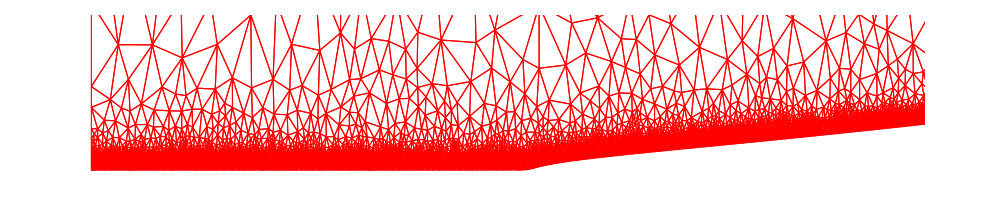

```mathematica
Show[{(*Ω^h["Wireframe"],*)(defΩ^h)["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[{Thin,Red}],FaceForm[]]]]},PlotRange->{{0.,0.5},{0,0.05}},ImageSize->1000](*13*)
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

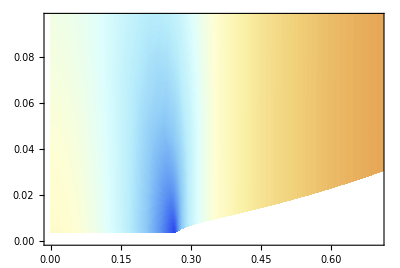

```mathematica
ContourPlot[Uz[x,y]+hshift,{x,y}∈Ω^h,ContourLines->False,ColorFunction->ColorData["LightTemperatureMap"],Contours->500,AspectRatio->0.67,PlotRange->{{0,0.7},{0,0.1},{-0.02,-0.}},PlotLegends->Automatic]/.(g_Graphics:>(g/.{x_?NumericQ,y_?NumericQ}:>Chop[(Through[{Ur,Uz}[x,y]]+{x,y})]))
```

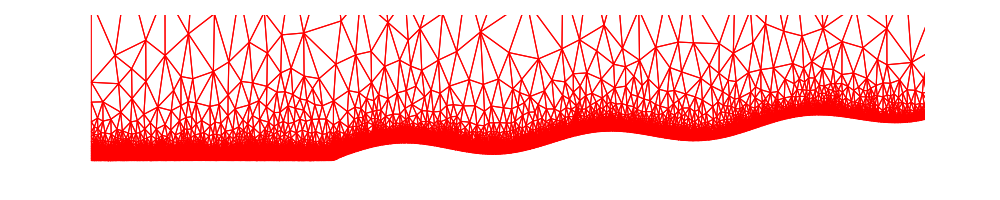

```mathematica
Show[{(*Ω^h["Wireframe"],*)(defΩ^h)["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[{Thin,Red}],FaceForm[]]]]},PlotRange->{{0.,0.5},{0,0.05}},ImageSize->1000](*30*)
```

```mathematica
Show[{(*Ω^h["Wireframe"],*)(defΩ^h)["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[{Thin,Red}],FaceForm[]]]]},PlotRange->{{0.,0.5},{0,0.05}},ImageSize->1000](*18*)
```

-Graphics-

## Strain and Stress

```mathematica
ϵ[r:_,z:_]=1/2(Grad[{Ur[r,z],0,Uz[r,z]},{r,θ,z},"Cylindrical"]+Transpose[Grad[{Ur[r,z],0,Uz[r,z]},{r,θ,z},"Cylindrical"]]);
```

```mathematica
Plot[ϵ[r,0.1][[3,3]],{r,0,width/2},PlotRange->All]
```

```mathematica
σrr=Function[{r,z},Ε/((1+ν)(1-2ν))((1-ν)(ϵ@@{r,z})[[1,1]]+ν(ϵ@@{r,z})[[2,2]]+ν(ϵ@@{r,z})[[3,3]])];
σθθ=Function[{r,z},Ε/((1+ν)(1-2ν))((1-ν)(ϵ@@{r,z})[[2,2]]+ν(ϵ@@{r,z})[[1,1]]+ν(ϵ@@{r,z})[[3,3]])];
σzz=Function[{r,z},Ε/((1+ν)(1-2ν))((1-ν)(ϵ@@{r,z})[[3,3]]+ν(ϵ@@{r,z})[[1,1]]+ν(ϵ@@{r,z})[[2,2]])];
σrz=Function[{r,z},Ε/((1+ν)(1-2ν))(1-2ν)(ϵ@@{r,z})[[1,3]]];
```

```mathematica
σrr@@{0.1,0.1}
```

```mathematica
Plot[σzz[r,ydatum+height],{r,0,2.5},PlotRange->All]
```

```mathematica
NIntegrate[2π r σzz[r,ydatum+height],{r,0,width/2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.97223891144336}. NIntegrate obtained 7074.74 and 9.65431 for the integral and error estimates.

7074.74

```mathematica
ContourPlot[σzz[r,z],{r,z}∈Ω^h,PlotLegends->Automatic,ContourLines->False,ColorFunction->ColorData["LightTemperatureMap"],Contours->50,AspectRatio->Automatic,PlotRange->All]
```

## Force and Contact radius

```mathematica
Pl=Table[0,{i,1,nStep}];
(*rl=Table[0,{i,1,nStep}];*)
```

```mathematica
For[ii=1,ii≤nStep,ii++,
UMat=SplitSolution[DisplUMat[[ii,;;]]];
(*UMat=SplitSolution[Un[[ii,;;]]];*)
{Ur,Uz}=Table[ElementMeshInterpolation[{Ω^h}, UMat[[;;,i]]//Normal],{i,1,Subscript[n, dof]}];

ϵ[r:_,z:_]=1/2(Grad[{Ur[r,z],0,Uz[r,z]},{r,θ,z},"Cylindrical"]+Transpose[Grad[{Ur[r,z],0,Uz[r,z]},{r,θ,z},"Cylindrical"]]);
σzz=Function[{r,z},Ε/((1+ν)(1-2ν))((1-ν)(ϵ@@{r,z})[[3,3]]+ν(ϵ@@{r,z})[[1,1]]+ν(ϵ@@{r,z})[[2,2]])];
Pl[[ii]]=NIntegrate[2π r σzz[r,ydatum+height],{r,0,width/2}];
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.97223891144336}. NIntegrate obtained 7016.47 and 13.4754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.97223891144336}. NIntegrate obtained 7028.78 and 13.4914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.97223891144336}. NIntegrate obtained 7034.3 and 13.4943 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Pl
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7016.47,7028.78,7034.3,7035.81,7034.12,7029.73,7024.04,7016.02,7002.58,6983.53,6962.42,6942.77,6925.63,6908.93,6890.03,6866.93,6838.5,6804.39,6765.2,6722.44,6677.67,6631.91,6585.73,6540.,6495.84,6453.68,6411.99,6367.85,6319.34,6266.63,6211.08,6153.56,6093.27,6028.84,5960.28,5889.08,5816.85,5744.51,5672.11,5599.27,5525.66,5451.75,5377.91,5304.86,5231.42,5156.35,5079.06,4999.73,4917.39,4830.67,4739.14,4643.8,4546.3,4448.16,4350.38,4252.57,4154.34,4055.32,3955.35,3854.23,3751.47,3646.66,3539.63,3430.45,3319.26,3206.88,3094.74,2983.87,2874.03,2763.49,2649.74,2531.,2407.84,2281.59,2153.73,2025.45,1897.01,1767.98,1639.04,1509.73,1380.18,1250.86,1119.73,985.224,852.894,715.153,577.157,437.683,296.72,155.593,12.3221,-130.133,-281.956,-432.178,-582.461,-732.144,-880.848,-1029.52,-1179.08,-1330.56,-1483.83,-1639.5}

```mathematica
Export["Pl.dat",{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7016.47308419518,7028.783250012927,7034.302497368495,7035.807480003612,7034.120383759584,7029.732050089736,7024.041400983338,7016.022294921091,7002.583700610597,6983.531498204213,6962.419391030098,6942.7674815078935,6925.630306639776,6908.93393343775,6890.034561291115,6866.934053513934,6838.499149031846,6804.385053054106,6765.204329703226,6722.441699564586,6677.674409363315,6631.913342544445,6585.727594546607,6539.99650503336,6495.83605741435,6453.675761931508,6411.985340578848,6367.853677461586,6319.335359558842,6266.626726081823,6211.078820903388,6153.557326408733,6093.274096938573,6028.843420755257,5960.283994001686,5889.081022135359,5816.84657839469,5744.513305465575,5672.1068708874955,5599.267672843288,5525.662256042769,5451.75486792713,5377.913423037222,5304.856466286992,5231.420155000065,5156.35444563122,5079.059578263043,4999.729840242964,4917.394549535715,4830.670222485396,4739.138511501957,4643.798020600043,4546.296294372924,4448.157771996405,4350.375384963119,4252.571654534204,4154.339933062318,4055.316851726842,3955.3504115950836,3854.2339366111873,3751.4670306019234,3646.6554163787873,3539.6333521833426,3430.447667052606,3319.2596290737897,3206.8825985080693,3094.737875737941,2983.8706469271383,2874.0341700042036,2763.493261751424,2649.7350916592413,2531.0043254991983,2407.842360207712,2281.5886757831086,2153.7329890957462,2025.4496341537451,1897.0061217640625,1767.9773354342633,1639.0422354668965,1509.726257220844,1380.1808110225074,1250.8609050862785,1119.7284015183295,985.2241236315563,852.8935441927241,715.153253900856,577.1568884332229,437.6825672269891,296.7203769374976,155.59296719352145,12.322148362391498,-130.13271008718928,-281.955543016623,-432.178300769797,-582.4612960559472,-732.1438253224178,-880.8483970182433,-1029.519625341011,-1179.0766632860214,-1330.5640005919727,-1483.8329246361889,-1639.4967659867298},"Table"]
```

Pl.dat

```mathematica
plt1=ListPlot[Thread[{hvec,-Pl}],Joined->True,PlotRange->All]
```

-Graphics-

-Graphics-

## Unloading step

```mathematica
unhvec=Range[6.5,-2.5,-0.1]*10^-3;
unStep=Length@unhvec
unDisplUMat=Table[0,{i,1,unStep},{j,1,Subscript[n, eq]}];
```

91

```mathematica
PrntlLoadLog[step_,iter_,nl_,dU_,dt_]:=Module[{},
loginfo=StringJoin[ToString[iter],"   Residual: ",ToString[nl,InputForm],"   Correction: ",ToString[dU,InputForm],"   time: ",ToString[dt],"\n"];
filename=FileNameJoin[{"Unload.log"}];
str=OpenAppend[filename];
If[iter==0,WriteString[str,StringJoin["Step ",ToString[step]," ",DateString[],"\n"]],WriteString[str,""]];
WriteString[str,loginfo];
Close[str]
]
```

```mathematica
hvec[[56]]
unhvec[[1]]
```

0.0065

0.0065

```mathematica
unDisplUMat[[1]]=DisplUMat[[56]];
(*unDisplUMat[[1]]=Un[[11]];*)
```

```mathematica
For[i=2,i≤unStep,i++,
β=0.30;
tol=10^-7;
err=1.0;
iter=0;
MaxIter=1000;
h=unhvec[[i]];
uOld=unDisplUMat[[i-1]];

ClearAll[KMat,fMat1];
ParallelEvaluate[KMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0]];
fMat1=SparseArray[{},{Subscript[n, eq]},0.0];

ParallelMap[ComputeElementStiffnessMatrix,Range[Subscript[n, el]]];

KList=Table[StringJoin["K",ToString[i]],{i,1,nKernel}];
KList=ParallelEvaluate[KMat];
KMatP =Apply[Plus,KList];
fMat1=0.5*fMat1;


While[err≥tol && iter≤MaxIter,
t1=AbsoluteTime[];
ClearAll[GMat,fMat2,fMat3,uMatNR];
uMatNR=SplitSolution[uOld];

ParallelEvaluate[GMat=SparseArray[{},{Subscript[n, eq],Subscript[n, eq]},0.0]];
fMat2=SparseArray[{},{Subscript[n, eq]},0.0];
ParallelEvaluate[fMat3=SparseArray[{},{Subscript[n, eq]},0.0]];

ParallelMap[ComputeElementStiffnessMatrixFromBodyforce,Table[{i,h},{i,1,Subscript[n, el]}]];
GList=Table[StringJoin["G",ToString[i]],{i,1,nKernel}];
GList=ParallelEvaluate[GMat];
GMatP =Apply[Plus,GList];
fMat2=0.5*fMat2;

ParallelMap[ComputeGlobalForceMatrixFromBodyforce,Table[{i,h},{i,1,Subscript[n, el]}]];
fList=Table[StringJoin["f",ToString[i]],{i,1,nKernel}];
fList=ParallelEvaluate[fMat3];
fMatP =Apply[Plus,fList];

KtMat=KMatP-GMatP;
ftMat=fMat1+fMat2+fMatP-KMatP.uOld;
dusol=LinearSolve[KtMat,ftMat];
uOld=uOld+β*dusol;

dt=AbsoluteTime[]-t1;
normftMat=Norm[ftMat,Infinity];
normdusol=Norm[dusol,Infinity];
PrntlLoadLog[i,iter,normftMat,normdusol,dt];
err=normdusol;
iter++;
];

unDisplUMat[[i]]=uOld;

OutputName=StringJoin["unUV",ToString[i],".dat"];
Export[OutputName,uOld,"Table"];
]
```

$Aborted

```mathematica
unPl=Table[0,{i,1,unStep}];
(*unrl=Table[0,{i,1,unStep}];*)
```

```mathematica
For[ii=1,ii≤48,ii++,
UMat=SplitSolution[unDisplUMat[[ii,;;]]];
(*UMat=SplitSolution[Un[[ii,;;]]];*)
{Ur,Uz}=Table[ElementMeshInterpolation[{Ω^h}, UMat[[;;,i]]//Normal],{i,1,Subscript[n, dof]}];

ϵ[r:_,z:_]=1/2(Grad[{Ur[r,z],0,Uz[r,z]},{r,θ,z},"Cylindrical"]+Transpose[Grad[{Ur[r,z],0,Uz[r,z]},{r,θ,z},"Cylindrical"]]);
σzz=Function[{r,z},Ε/((1+ν)(1-2ν))((1-ν)(ϵ@@{r,z})[[3,3]]+ν(ϵ@@{r,z})[[1,1]]+ν(ϵ@@{r,z})[[2,2]])];
unPl[[ii]]=NIntegrate[2π r σzz[r,ydatum+height],{r,0,width/2}];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.97223891144336}. NIntegrate obtained 7024.04 and 13.4711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.97223891144336}. NIntegrate obtained 7029.68 and 13.4901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {2.97223891144336}. NIntegrate obtained 7034.08 and 13.5065 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
unPl
```

{7024.04,7029.68,7034.08,7035.77,7034.25,7028.74,7016.44,6994.58,6968.89,6945.26,6920.43,6890.27,6855.76,6821.97,6790.17,6758.42,6721.06,6671.23,6616.48,6563.21,6502.86,6431.63,6349.19,6260.16,6168.1,6063.03,5944.98,5825.28,5687.73,5534.84,5368.41,5208.93,5004.43,4682.54,4321.87,3759.35,27.6885,22.054,17.3527,13.4959,10.3382,7.79274,5.74496,4.13588,2.89161,1.94331,1.25092,0.758542,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Export["unPl.dat",{7024.041400983338,7029.684808415989,7034.075584028798,7035.766106799503,7034.252138342132,7028.738151566251,7016.435825777308,6994.58421134904,6968.8883775863505,6945.258816386607,6920.430863039025,6890.265103058052,6855.759473058221,6821.967912809909,6790.165441932895,6758.416765807887,6721.0551523711365,6671.233538888815,6616.477265389692,6563.208863979545,6502.856925380606,6431.632486032653,6349.188315357091,6260.1588186494855,6168.095457054013,6063.027931778958,5944.975484174126,5825.280984996377,5687.726581644803,5534.8379342129765,5368.4111800902765,5208.928702810845,5004.428907874232,4682.53676619126,4321.865220127564,3759.3453519664395,27.68853286316176,22.05403590289504,17.35266665284207,13.4958813709925,10.338152813694345,7.792742595609638,5.74496026197644,4.135882134912845,2.891608493035556,1.943311340612185,1.250923739330287,0.7585423872569702,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},"Table"]
```

unPl.dat

```mathematica
plt2=ListPlot[Thread[{unhvec,-unPl}],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Show[plt1,plt2,PlotRange->All]
```

-Graphics-

## Split Solution

```mathematica
ii=1;
hshift=-(141-ii)/10^4;
InputName=StringJoin["unUV",ToString[ii],".dat"];
Un=Flatten[Import[InputName]];
```

```mathematica
UMat=SplitSolution[Un];
{Ur,Uz}=Table[ElementMeshInterpolation[{Ω^h}, UMat[[;;,i]]//Normal],{i,1,Subscript[n, dof]}];
```

## Deformed mesh

```mathematica
defΩ^h=ElementMeshDeformation[Ω^h,{Ur,Uz}];
```

```mathematica
qd=(defΩ^h)["Quality"];
{Min/@qd,Mean/@qd,StandardDeviation/@qd}
```

{{0.513417},{0.911166},{0.0783159}}

```mathematica
Show[{(*Ω^h["Wireframe"],*)(defΩ^h)["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[{Thin,Red}],FaceForm[]]]]},PlotRange->{{0.,0.5},{0,0.05}},ImageSize->1000](*76*)
```

-Graphics-

```mathematica
ContourPlot[Uz[x,y]+hshift,{x,y}∈Ω^h,ContourLines->False,ColorFunction->ColorData["LightTemperatureMap"],Contours->500,AspectRatio->0.67,PlotRange->{{0,0.7},{0,0.1},{-0.02,0.}},PlotLegends->Automatic]/.(g_Graphics:>(g/.{x_?NumericQ,y_?NumericQ}:>Chop[(Through[{Ur,Uz}[x,y]]+{x,y})]))
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[{(*Ω^h["Wireframe"],*)(defΩ^h)["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[{Thin,Red}],FaceForm[]]]]},PlotRange->{{0.,0.5},{0,0.05}},ImageSize->1000](*80*)
```

-Graphics-

```mathematica
ContourPlot[Uz[x,y]+hshift,{x,y}∈Ω^h,ContourLines->False,ColorFunction->ColorData["LightTemperatureMap"],Contours->500,AspectRatio->0.67,PlotRange->{{0,0.7},{0,0.1},{-0.02,0.}},PlotLegends->Automatic]/.(g_Graphics:>(g/.{x_?NumericQ,y_?NumericQ}:>Chop[(Through[{Ur,Uz}[x,y]]+{x,y})]))
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[{(*Ω^h["Wireframe"],*)(defΩ^h)["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[{Thin,Red}],FaceForm[]]]]},PlotRange->{{0.,0.5},{0,0.05}},ImageSize->1000](*96*)
```

-Graphics-

```mathematica
ContourPlot[Uz[x,y]+hshift,{x,y}∈Ω^h,ContourLines->False,ColorFunction->ColorData["LightTemperatureMap"],Contours->500,AspectRatio->0.67,PlotRange->{{0,0.7},{0,0.1},{-0.02,0.}},PlotLegends->Automatic]/.(g_Graphics:>(g/.{x_?NumericQ,y_?NumericQ}:>Chop[(Through[{Ur,Uz}[x,y]]+{x,y})]))
```

InterpolatingFunction::femdmval: Input value {0.,0.} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

-Graphics-